best config found :

doundboard thickness : 0.499663 mm

bar thickness : 0.994483 mm

bracing type : parallel

max predicted SPL : 0.0946058

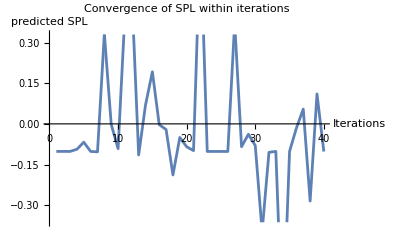

```mathematica
sounddata=Import["C:\\Users\\akrem\\Desktop\\work\\soundboard\\soundboard_data.xlsx"][[1]];
traininput=sounddata[[2;;,{1,2,3}]];
trainout=sounddata[[2;;,4]];
train=Thread[Rule[traininput,trainout]];

predictor=Predict[train,Method->{"GaussianProcess","CovarianceType"-><|"Numerical"->"SquaredExponential","Nominal"->"HammingDistance"|>,"EstimationMethod"->"MaximumLikelihood"},PerformanceGoal->"Quality"];

(*---domain of data---*)
sbThicknessRange=MinMax[traininput[[All,1]]];
barThicknessRange=MinMax[traininput[[All,2]]];
bracingTypes=Union[traininput[[All,3]]];

(*---objectif funct---*)
objectiveSPL[config_]:=predictor[config];

(*---mixed cinfig generator (numeric+nominal)---*)
configSampler[]:={RandomReal[sbThicknessRange],RandomReal[barThicknessRange],RandomChoice[bracingTypes]};

(*---Optimisation bayésienne---*)
boSPL=BayesianMaximization[objectiveSPL,configSampler,Method->"MaxExpectedImprovement",MaxIterations->40];

(*---Resuls---*)
bestConfig=boSPL["MaximumConfiguration"];
bestSPL=boSPL["MaximumValue"];

Print["best config found :"];
Print["  doundboard thickness : ",bestConfig[[1]]," mm"];
Print["  bar thickness : ",bestConfig[[2]]," mm"];
Print["  bracing type : ",bestConfig[[3]]];
Print[" max predicted SPL : ",bestSPL];

(*Visualisation of convergence*)
ListLinePlot[Normal[boSPL["EvaluationHistory"]][[All,"Value"]],PlotLabel->"Convergence of SPL within iterations",AxesLabel->{"Iterations"," predicted SPL"}]
```

```mathematica
Information[predictor,"InternalParameters"]
```

{HammingDistance→<|CategoricalLengthScale→0.11206,SignalStandardDeviation→3.47928|>,SquaredExponential→<|NumericalLengthScale→0.199352,SignalVariance→0.262686|>,WN→<|NoiseVariance→0.00138062|>}

```mathematica
boSPL["EvaluationHistory"]
```